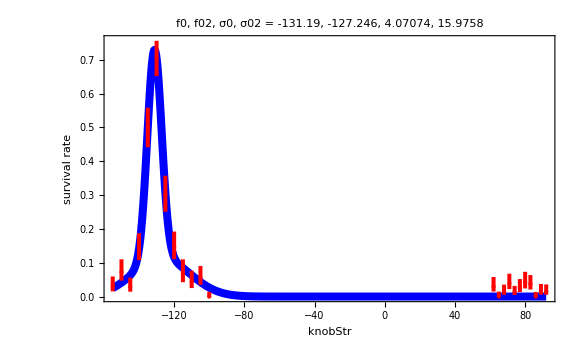

```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]
dat={{{-155.,0.030303030303030304},ErrorBar[{-0.015074076207857643,0.029094881273438823}]},{{-150.,0.07246376811594203},ErrorBar[{-0.025475340524504272,0.03769066143547735}]},{{-145.,0.02857142857142857},ErrorBar[{-0.014216919883529282,0.02749659795193975}]},{{-140.,0.14285714285714285},ErrorBar[{-0.035306376813887486,0.04446388597139664}]},{{-135.,0.5},ErrorBar[{-0.05852057359806534,0.05852057359806517}]},{{-130.,0.7066666666666667},ErrorBar[{-0.05501537805151879,0.04957678156029077}]},{{-125.,0.3013698630136986},ErrorBar[{-0.05072387975307707,0.05609226183378796}]},{{-120.,0.14666666666666667},ErrorBar[{-0.036196904767346716,0.04549515038138177}]},{{-115.,0.06896551724137931},ErrorBar[{-0.026482873141523304,0.041094211540120634}]},{{-110.,0.04411764705882353},ErrorBar[{-0.018982661585342942,0.032196642830014714}]},{{-105.,0.056338028169014086},ErrorBar[{-0.021701257453608583,0.03402520111558042}]},{{-100.,0.},ErrorBar[{0.,0.013888888888888888}]},{{62.,0.029411764705882353},ErrorBar[{-0.014632957429090569,0.028273196133267904}]},{{65.,0.},ErrorBar[{0.,0.014705882352941176}]},{{68.,0.0136986301369863},ErrorBar[{-0.00845391254730036,0.0215971928138683}]},{{71.,0.03896103896103896},ErrorBar[{-0.016782337234845415,0.028603849056357253}]},{{74.,0.012195121951219513},ErrorBar[{-0.007527252036975169,0.019281586447789153}]},{{77.,0.02631578947368421},ErrorBar[{-0.013099585926873084,0.0254030719145696}]},{{80.,0.04225352112676056},ErrorBar[{-0.018187811686331073,0.030902991655032172}]},{{83.,0.036585365853658534},ErrorBar[{-0.015766972292034245,0.02693358998230754}]},{{86.,0.},ErrorBar[{0.,0.013513513513513514}]},{{89.,0.014492753623188406},ErrorBar[{-0.00894323556675688,0.022814871177522927}]},{{92.,0.013888888888888888},ErrorBar[{-0.008571153802275114,0.021889266435456238}]}};
gauss2=A Exp[-(f-f0)^2/(2 σ0^2)]+A2 Exp[-(f-f02)^2/(2 σ02^2)]+0 offs;

(*which data to fit*)
datfit=Cases[dat,x_/;x[[1,1]]<-100||x[[1,1]]>10000];

{offs0,A0,f00,σ00,A200,f020,σ020}={0,.7,-160,5,.1,-120,5};(*axis 3*)
{offs0,A0,f00,σ00,A200,f020,σ020}={0,.3,-31,3,.25,-10,3};(*axis 1*)
{offs0,A0,f00,σ00,A200,f020,σ020}={0,.7,-130,4,.1,-118,1};(*axis 2*)
nlm=NonlinearModelFit[datfit[[;;,1]],gauss2,{{ offs,offs0},{ A,A0}, {f0,f00}, {σ0,σ00},{ A2,A200}, {f02,f020}, {σ02,σ020}},f(*,Weights->weights*)];
fit=nlm["BestFitParameters"];

Show[{
Plot[
gauss2/.fit,{f,dat[[1,1,1]],dat[[-1,1,1]]},PlotStyle->{Thickness[.01],Blue},Frame->{True,True},Axes->False,FrameLabel->{knobStr,"survival rate"},PlotRange->All,PlotLabel->"f0, f02, σ0, σ02 = " <>ToString[f0/.fit]<>", "<>ToString[f02/.fit]<>", "<>ToString[σ0/.fit]<>", "<>ToString[σ02/.fit] 
],

ErrorListPlot[dat,PlotStyle->{Thickness[.005],Red},Frame->{True,True},Axes->False]
}]
```

```mathematica
fit
BSBdat=Cases[dat,x_/;x[[1,1]]>0&&x[[1,1]]<1000];
Δf=Mean[Differences[BSBdat[[;;,1]][[;;,1]]]];
ARSB=A √(2 π)σ0;
nbar=1/(ARSB/ABSB-1);
Δnbar=√((D[nbar, σ0])^2(#[[4]])^2+(D[nbar, A])^2(#[[2]])^2+(D[nbar, ABSB])^2 ΔABSB^2)&@nlm["ParameterErrors"]/.fit;
Δbsb=Flatten[Differences[#]&/@Cases[ToExpression[StringSplit[ToString[BSBdat[[;;,2]]],{"ErrorBar[","]"}]],x_/;Head[x]==List]];
ΔABSB=Sqrt[Total[(Δbsb/Length[Δbsb])^2]];
ABSB=Total[BSBdat[[;;,1]][[;;,2]]-offs/.fit]Δf;


nbar/.fit
Δnbar
```

{offs→0.,A→0.619466,f0→-131.19,σ0→4.07074,A2→0.113285,f02→-127.246,σ02→15.9758}

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before ", ".
                                                  ^

General::stop: 
   Further output of ToExpression::sntx
     will be suppressed during this calculation.

0.121225

0.0169405